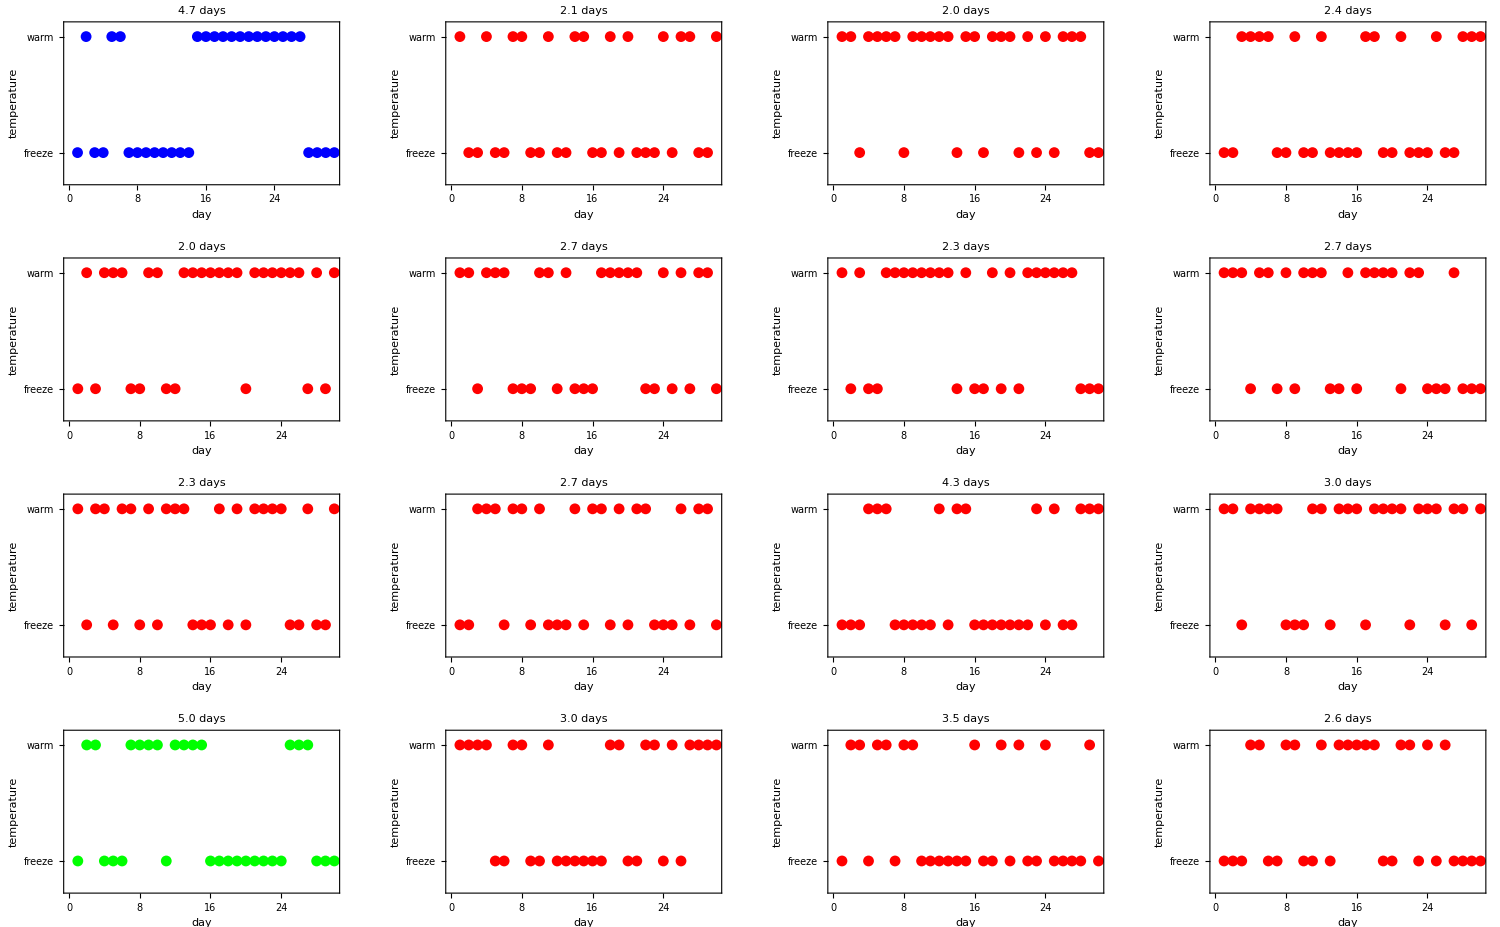

Evaluation_snowDays.pdf

```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
p=DiscreteMarkovProcess[{1,0},{{0.85,0.15},{0.3,0.7}}];
n = 30;
data= Flatten[ Normal@RandomFunction[p,{0,n}],1][[All,2]];
fPlotReal[data_]:=Module[{yTicks= {{2,"warm"},{1,"freeze"}},realMeanWet= N@Mean@(Length/@Cases[Split@data,{1,__}])},
ListPlot[data,PlotStyle->Blue,Frame->{True,True,False,False},FrameLabel->{"day","temperature"},BaseStyle->{FontSize->16},FrameTicks->{True,yTicks},PlotRange->{Full,{0.75,2.1}},PlotLabel->StringJoin[ToString@PaddedForm[realMeanWet,{2,1}]," days"]]]
fDataPlotter[data_,n_Integer]:=Module[{yTicks= {{2,"warm"},{1,"freeze"}},realMeanWet= N@Mean@(Length/@Cases[Split@data,{1,__}]),dataFake = 1+RandomVariate[BernoulliDistribution[Total@(If[#==2,1,0]&/@data)/n],{n}],numFake,aColour},
numFake = N@Mean@(Length/@Cases[Split@dataFake,{1,__}]);
aColour = If[numFake<realMeanWet,Red,Green];
ListPlot[dataFake,PlotStyle->aColour,Frame->{True,True,False,False},FrameLabel->{"day","temperature"},BaseStyle->{FontSize->16},FrameTicks->{True,yTicks},PlotRange->{Full,{0.75,2.1}},PlotLabel->StringJoin[ToString@PaddedForm[numFake,{2,1}]," days"]]]
gFinal=Show[GraphicsGrid[{{fPlotReal[data],fDataPlotter[data,n],fDataPlotter[data,n],fDataPlotter[data,n]},{fDataPlotter[data,n],fDataPlotter[data,n],fDataPlotter[data,n],fDataPlotter[data,n]},{fDataPlotter[data,n],fDataPlotter[data,n],fDataPlotter[data,n],fDataPlotter[data,n]},{fDataPlotter[data,n],fDataPlotter[data,n],fDataPlotter[data,n],fDataPlotter[data,n]}}],ImageSize->1500]
Export["Evaluation_snowDays.pdf",gFinal]
```